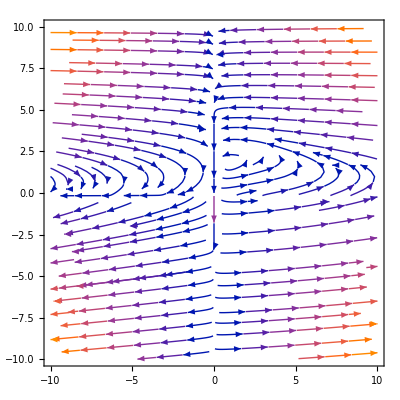

```mathematica
(*Define the functions*)G[u_,v_,J_,K_]:=Module[{numerator,den1,den2,radicand,denominator},numerator=2*u*K;
den1=v-u+v*J+u*K;
den2=-4*(v-u)*u*K;
radicand=den1^2+den2;
denominator=den1+Sqrt[radicand];
numerator/denominator]

ACp[cAMP_,ACt_,r1_,r2_,Dvalue_,Km1_,Km2_]:=ACt*G[r1*cAMP,r2*Dvalue,Km1/ACt,Km2/ACt]

dcAMP[cAMP_,ACp_,k1_,k3_,k2_,PDEp_]:=k1*ACp-(k3+k2*PDEp)*cAMP

dPDEp[cAMP_,PDEt_,PDEp_,r3_,Et_,Km3_,Km4_,r4_]:=r3*cAMP*((PDEt-PDEp)/Km3)-r4*Et*PDEp/(Km4+PDEp)

(*Set the parameters*)
k1=9.18;
k3=0.12;
k2=10;
r1=2.04;
r2=9.34;
r3=0.56;
r4=1.84;
Km1=0.46;
Km2=9.34;
Km3=1.26;
Km4=0.18;
Dvalue=1.26;
ACt=10;
PDEt=9.66;
Et=2.04;

(*Define the system*)
system[cAMP_,PDEp_]:={dcAMP[cAMP,ACp[cAMP,ACt,r1,r2,Dvalue,Km1,Km2],k1,k3,k2,PDEp],dPDEp[cAMP,PDEt,PDEp,r3,Et,Km3,Km4,r4]}

(*Generate a stream plot*)
StreamPlot[system[cAMP,PDEp],{cAMP,-10,10},{PDEp,-10,10}]
```

```mathematica
(*Define the functions*)G[u_,v_,J_,K_]:=Module[{numerator,den1,den2,radicand,denominator},numerator=2*u*K;
den1=v-u+v*J+u*K;
den2=-4*(v-u)*u*K;
radicand=den1^2+den2;
denominator=den1+Sqrt[radicand];
numerator/denominator]

ACp[cAMP_,ACt_,r1_,r2_,Dvalue_,Km1_,Km2_]:=ACt*G[r1*cAMP,r2*Dvalue,Km1/ACt,Km2/ACt]

dcAMP[cAMP_,ACp_,k1_,k3_,k2_,PDEp_]:=k1*ACp-(k3+k2*PDEp)*cAMP

dPDEp[cAMP_,PDEt_,PDEp_,r3_,Et_,Km3_,Km4_,r4_]:=r3*cAMP*((PDEt-PDEp)/Km3)-r4*Et*PDEp/(Km4+PDEp)

(*Set the parameters*)
k1=9.18;
k3=0.12;
k2=10;
r1=2.04;
r2=9.34;
r3=0.56;
r4=1.84;
Km1=0.46;
Km2=9.34;
Km3=1.26;
Km4=0.18;
Dvalue=1.26;
ACt=10;
PDEt=9.66;
Et=2.04;

(*Define the system*)
system[cAMP_,PDEp_]:={dcAMP[cAMP,ACp[cAMP,ACt,r1,r2,Dvalue,Km1,Km2],k1,k3,k2,PDEp],dPDEp[cAMP,PDEt,PDEp,r3,Et,Km3,Km4,r4]}

(*Find the fixed points*)
fixedPoints=NSolve[system[cAMP,PDEp]=={0,0},{cAMP,PDEp},Reals]

(*Calculate the Jacobian matrix*)
jacobianMatrix=D[system[cAMP,PDEp],{{cAMP,PDEp}}]

(*Print the Jacobian matrix*)
Print[jacobianMatrix]

(*Calculate the eigenvalues*)
eigenvaluesList=Eigenvalues[jacobianMatrix/. #]&/@fixedPoints

(*Print the eigenvalues*)
Print[eigenvaluesList]
```

{{cAMP→0.951867,PDEp→1.65682},{cAMP→0.,PDEp→0.}}

{{-0.12-(349.824 cAMP (-0.13464+(-7.62144 (11.7684-2.04 cAMP)-0.26928 (12.3097-0.13464 cAMP)+15.5477 cAMP)/(2 √((12.3097-0.13464 cAMP)^2-7.62144 (11.7684-2.04 cAMP) cAMP))))/((12.3097-0.13464 cAMP+√((12.3097-0.13464 cAMP)^2-7.62144 (11.7684-2.04 cAMP) cAMP))^2)+349.824/(12.3097-0.13464 cAMP+√((12.3097-0.13464 cAMP)^2-7.62144 (11.7684-2.04 cAMP) cAMP))-10 PDEp,-10 cAMP},{0.444444 (9.66-PDEp),-0.444444 cAMP+(3.7536 PDEp)/(0.18+PDEp)^2-3.7536/(0.18+PDEp)}}

{{-0.12-(349.824 cAMP (-0.13464+(-7.62144 (11.7684-2.04 cAMP)-0.26928 (12.3097-0.13464 cAMP)+15.5477 cAMP)/(2 √((12.3097-0.13464 cAMP)^2-7.62144 (11.7684-2.04 cAMP) cAMP))))/((12.3097-0.13464 cAMP+√((12.3097-0.13464 cAMP)^2-7.62144 (11.7684-2.04 cAMP) cAMP))^2)+349.824/(12.3097-0.13464 cAMP+√((12.3097-0.13464 cAMP)^2-7.62144 (11.7684-2.04 cAMP) cAMP))-10 PDEp,-10 cAMP},{0.444444 (9.66-PDEp),-0.444444 cAMP+(3.7536 PDEp)/(0.18+PDEp)^2-3.7536/(0.18+PDEp)}}

{{1.10663+5.55562 ⅈ,1.10663-5.55562 ⅈ},{-20.8533,14.0892}}

{{1.10663+5.55562 ⅈ,1.10663-5.55562 ⅈ},{-20.8533,14.0892}}